```mathematica
(*with rfd, 5000 non interacting particles*)
(*SetDirectory[NotebookDirectory[]];
raw0=Import["0_asciiMeans000500000","Table"];
raw1=Import["1_asciiMeans000500000","Table"];
raw2=Import["2_asciiMeans000500000","Table"];.
raw3=Import["3_asciiMeans000500000","Table"];

raw=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]]];*)

SetDirectory[NotebookDirectory[]];
raw0=Import["0_asciiEy000000001","Table"];
(*raw1=Import["1_asciiMeans000500000","Table"];*)


raw=raw0[[1;;-3]]
```

{{(0,0,0),-88.1808},{(1,0,0),-265.07},{(2,0,0),-443.543},{(3,0,0),-624.653},{(4,0,0),-809.448},{(5,0,0),-998.968},{(6,0,0),-1194.24},{(7,0,0),-1396.26},{(8,0,0),-1606},{(9,0,0),-1824.37},2097133,{(119,127,127),1519.55},{(120,127,127),1324.16},{(121,127,127),1134.87},{(122,127,127),950.955},{(123,127,127),771.66},{(124,127,127),596.183},{(125,127,127),423.695},{(126,127,127),253.355},{(127,127,127),84.308}}
 |  |  |  |

```mathematica
xs = 16*10^-7;
ys = 16*10^-7;
zs = 16*10^-7;
dx = xs/128;
dy = ys/128;
dz = zs/128;

members3D=Table[{ToExpression[StringReplace[raw[[ii,1]],{"("-> "{",")"-> "}"}]],raw[[ii,2]]},{ii,1,Length[raw]}]
members3DReal=Table[{{members3D[[ii,1,1]]*(dx)+dx/2,members3D[[ii,1,2]]*(dy)+dy/2,members3D[[ii,1,3]]*(dz)+dz/2},members3D[[ii,2]]},{ii,1,Length[members3D]}]
func3D=Interpolation[members3DReal];
```

{{{0,0,0},-88.1808},{{1,0,0},-265.07},{{2,0,0},-443.543},{{3,0,0},-624.653},{{4,0,0},-809.448},{{5,0,0},-998.968},{{6,0,0},-1194.24},{{7,0,0},-1396.26},{{8,0,0},-1606},{{9,0,0},-1824.37},{{10,0,0},-2052.2},2097131,{{118,127,127},1721.69},{{119,127,127},1519.55},{{120,127,127},1324.16},{{121,127,127},1134.87},{{122,127,127},950.955},{{123,127,127},771.66},{{124,127,127},596.183},{{125,127,127},423.695},{{126,127,127},253.355},{{127,127,127},84.308}}
 |  |  |  |

{{{1/160000000,1/160000000,1/160000000},-88.1808},{{3/160000000,1/160000000,1/160000000},-265.07},{{1/32000000,1/160000000,1/160000000},-443.543},{{7/160000000,1/160000000,1/160000000},-624.653},{{9/160000000,1/160000000,1/160000000},-809.448},2097142,{{247/160000000,51/32000000,51/32000000},771.66},{{249/160000000,51/32000000,51/32000000},596.183},{{251/160000000,51/32000000,51/32000000},423.695},{{253/160000000,51/32000000,51/32000000},253.355},{{51/32000000,51/32000000,51/32000000},84.308}}
 |  |  |  |

```mathematica
xx=32*dx;
yy=16.01*dx
zz=16*dx;

func3D[xx,yy,zz]
```

2.00125×10^-7

3135.45

InterpolatingFunction::dmval: Input value {1/2500000,2.85714×10^-11,2.85714×10^-11} lies outside the range of data in the interpolating function. Extrapolation will be used.

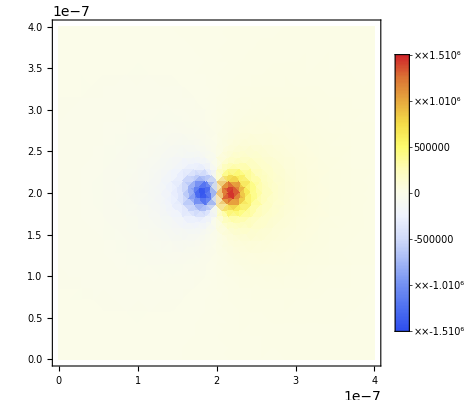

```mathematica
DensityPlot[func3D[xx,y,z],{y,0,ys/4},{z,0,zs/4},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All]
```

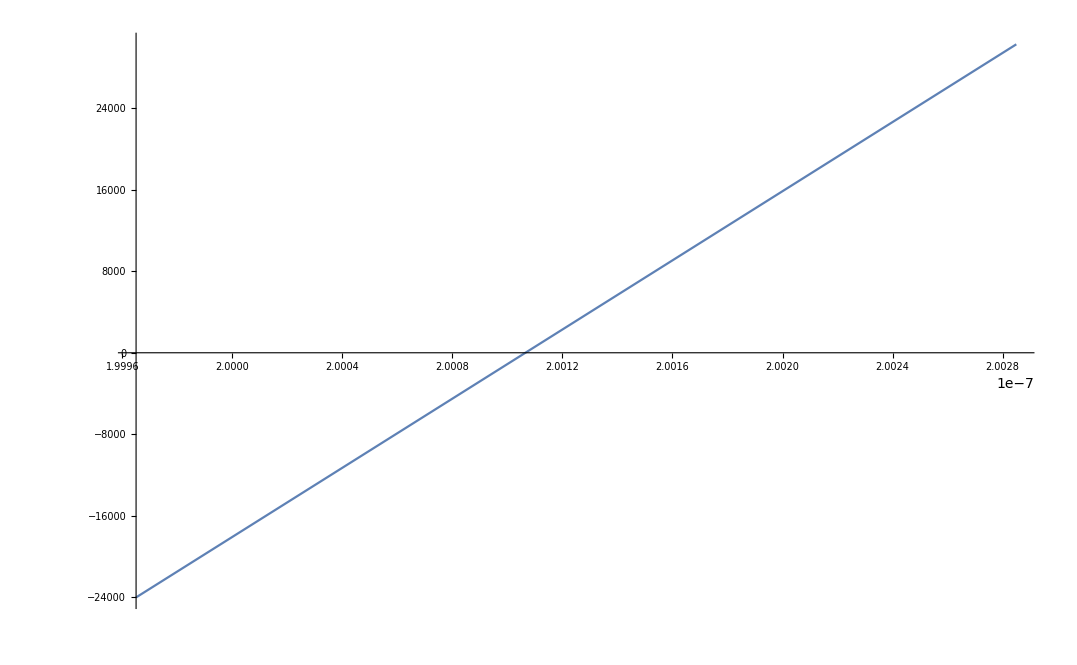

```mathematica
Plot[func3D[xx,y,zz],{y,yy-ys/10000,yy+ys/10000}]
```

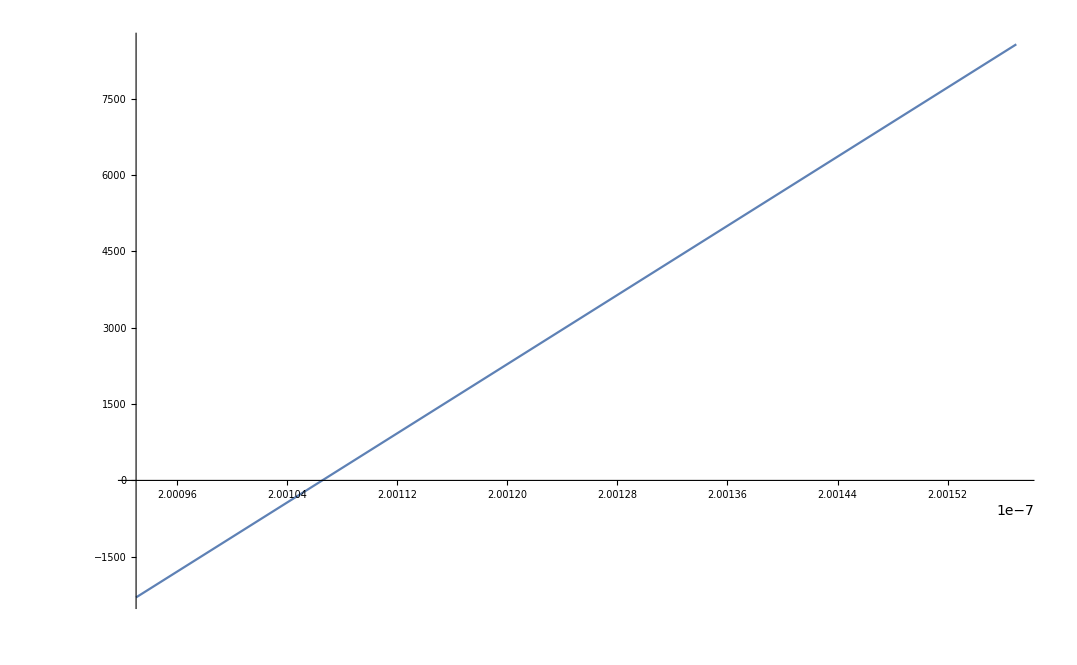

```mathematica
a cf==(q b)^2/r^2
```

a cf==(b+q)^2/r^2